# Numerical solution of Schrödinger equation for arbitrary N-dimensional potentials

## Jens Uwe Nöckel, University of Oregon [http://pages.uoregon.edu/noeckel/]. http://mathematica.stackexchange.com/questions/50763/schroedinger-eigenvalue-problem-in-two-dimensions-harmonic-oscillator

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Codes/MathPCET

## test the new MathPCET package

```mathematica
Needs["MathPCET`"]
```

## Simple approach

```mathematica
?GridSolverND
```

GridSolverND[vGrid, delta, n]
The input parameters:
vGrid - N-dimensional matrix of the potential values (atomic units) on the N-dimensional grid;
delta - grid size (in atomic units), the same in each dimension;
n - number of lowest eigenvalues (and eigenvectors) desired;
Options:
M -> mass of the particle in electron mass units (Daltons)
Output:
Returns a nested list of the following structure:
(
   (energyLevel_1, energyLevel_2, ..., energyLevel_n),
   (
      (wavefunctionGrid_1, wavefunctionGrid_2, ..., wavefunctionGrid_n)
   )
)

### Test one-dimensional harmonic oscillator:

```mathematica
xx=10.0;
nX=128;
dx=xx/(2nX)
v1[x_]:=1/2 x^2-10;
v1Grid=Table[v1[dx i],{i,-nX,nX}];
```

0.0390625

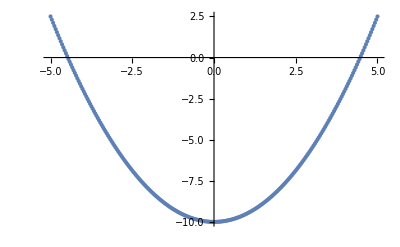

```mathematica
ListPlot[v1Grid,DataRange->{-nX dx,nX dx}]
```

```mathematica
sol1D=GridSolverND[v1Grid,dx,5,M->1];
```

```mathematica
sol1D⟦1⟧
```

{-9.50005,-8.50024,-7.50062,-6.50119,-5.50195}

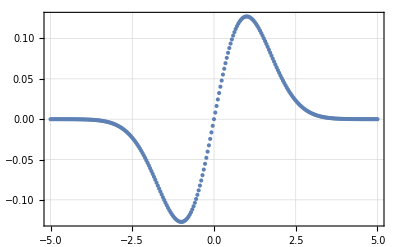

```mathematica
ListPlot[sol1D⟦2,2⟧,PlotRange->All,PlotTheme->"Detailed",DataRange->{-nX dx,nX dx}]
```

### Test two-dimensional harmonic oscillator:

```mathematica
nX=100;
nY=100;
a=.05;
```

```mathematica
v2[x_,y_]:=1/2(x^2+y^2)-10;
```

```mathematica
v2Grid=Table[v2[a i,a j],{i,-nX,nX},{j,-nY,nY}];
```

```mathematica
sol2D=GridSolverND[v2Grid,a,5];
```

```mathematica
sol2D⟦1⟧
```

{-9.00016,-8.00047,-8.00047,-7.00109,-7.00078}

```mathematica
ListContourPlot[sol2D⟦2,2⟧,PlotRange->All,Axes->False,DataRange->{{-a nX,a nX},{-a nX,a nX}}]
```

-Graphics-

```mathematica
ListPlot3D[-sol2D⟦2,2⟧,PlotRange->All,Boxed->False,Axes->False]
```

-Graphics3D-

### Test three-dimensional harmonic oscillator:

```mathematica
nX=16;
nY=16;
nZ=16;
a=0.3;
```

```mathematica
v3[x_,y_,z_]:=1/2(x^2+y^2+z^2);
```

```mathematica
v3Grid=Table[v3[a i,a j,a k],{i,-nX,nX},{j,-nY,nY},{k,-nZ,nZ}];
```

```mathematica
sol3D=GridSolverND[v3Grid,a,5];
```

```mathematica
sol3D⟦1⟧
```

{1.49151,2.48013,2.48013,3.4572,3.46875}

## General approach with an arbitrary difference order for the numerical second derivative

```mathematica
?GenGridSolverND
```

GenGridSolverND[vGrid, delta, n]
The input parameters:
vGrid - N-dimensional matrix of the potential values (atomic units) on the N-dimensional grid;
delta - grid size (in atomic units), the same in each dimension;
n - number of lowest eigenvalues (and eigenvectors) desired;
Options:
M -> mass of the particle in Daltons (default is mass of an electron = 1 Dalton)
DiffOrder -> accuracy order for the nnnumerical second derivatrive on the grid (default is 4)
Output:
Returns a nested list of the following structure:
(
   (energyLevel_1, energyLevel_2, ..., energyLevel_n),
   (
      (wavefunctionGrid_1, wavefunctionGrid_2, ..., wavefunctionGrid_n)
   )
)

### Test 2D harmonic oscillator:

```mathematica
nX=200;
nY=200;
a=.025;
Clear[v2];
v2[x_,y_]:=1/2(x^2+y^2+x y)-10;
v2Grid=Table[v2[a i,a j],{i,-nX,nX},{j,-nY,nY}];
```

```mathematica
sol2ND=GenGridSolverND[v2Grid,a,5,DiffOrder->4];
```

```mathematica
sol2ND⟦1⟧
```

{-9.03407,-8.32697,-7.80933,-7.61986,-7.10222}

```mathematica
GraphicsRow[{
ListContourPlot[sol2ND⟦2,4⟧,PlotRange->All,ColorFunction->"DarkRainbow"],
ListContourPlot[sol2ND⟦2,5⟧,PlotRange->All,ColorFunction->"DarkRainbow"]
},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[{
ListPlot3D[sol2ND⟦2,4⟧,PlotRange->All,Boxed->False,Axes->False,Mesh->25,ColorFunction->"DarkRainbow"],
ListPlot3D[sol2ND⟦2,5⟧,PlotRange->All,Boxed->False,Axes->False,Mesh->25,ColorFunction->"DarkRainbow"]
},ImageSize->Large]
```

-Graphics-

## Test FGH vibronic couplings

```mathematica
?FGHVibronicCouplings
```

Fourier Grid Hamiltonian calculations of the wavefunctions, overlap integrals, and vibronic couplings (electronically nonadiabatic, electronically adiabatic, and semiclassical approximations).
FGHWavefunctions[file_,nGridPoints_,nStates_].
Parameters:
file - name of the file with the potential data (four columns: x(A) Ureactant(kcal/mol) Uproduct(kcal/mol) ElectronicCoupling (kcal/mol));
nGridPoints - number of grid points (should be power of two);
nStates - number of vibrational states in each well to calculate.
Options:
M -> mass of the particle in Daltons (Default - mass of the proton).
Output:
Returns a nested list of the following structure:
(
 (reactantEnergies_list, reactantPotential_matrix, reactantWavefunctions_matrix),
 (productEnergies_list, productPotential_matrix, productWavefunctions_matrix),
 overlap_matrix,
 diabatic_coupling_matrix,
 product_coupling_matrix,
 semiclassical_coupling_matrix,
 half_tunneling_splitting_matrix,
 tau_e_matrix,
 tau_p_matrix,
 adiabaticity_parameter_matrix,
 kappa_matrix
)
where
xxxEnergies_list - is a list (vector) of length nStates;
xxxPotential_matrix - a 2D-list (table) of the splined potential [nGridPoints by 2];
xxxWavefunctions_matrix - a 2D-list (matrix)  [nStates by nGridPoints];
overlap_matrix - 2D-list (matrix) of overlap integrals [nStates by nStates];
diabatic_coupling_matrix - 2D-list (matrix) of vibronic couplings V_μν=<χ_μ|V^el(x)|χ_ν> (kcal/mol) [nStates by nStates].;
product_coupling_matrix - 2D-list (matrix) of vibronic couplings V_μν=V^el<χ_μ|χ_ν> (kcal/mol) [nStates by nStates].;
semiclassical_coupling_matrix - 2D-list (matrix) of semiclassical vibronic couplings (kcal/mol) (Georgievskii-Stuchebrukhov) [nStates by nStates].;
half_tunneling_splitting_matrix - 2D-list (matrix) of half tunneling splittings (kcal/mol) (electronically adiabatic approximation) [nStates by nStates].;
tau_e_matrix - 2D-list (matrix) of electronic transition times (fs) [nStates by nStates].;
tau_p_matrix - 2D-list (matrix) of proton tunneling times (fs) [nStates by nStates].;
adiabaticity_parameter_matrix - 2D-list (matrix) of adiabaticity parameters p [nStates by nStates].;
kappa_matrix - 2D-list (matrix) of prefactors κ [nStates by nStates].

```mathematica
testSolution=FGHVibronicCouplings["potential.dat",256,5];
```

```mathematica
potentialLeft=testSolution⟦1⟧⟦2⟧;
potentialRight=testSolution⟦2,2⟧;
```

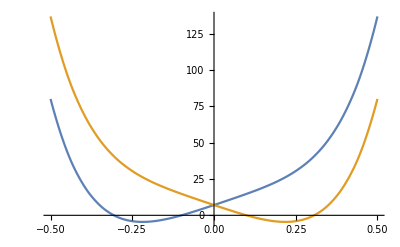

```mathematica
ListLinePlot[{potentialLeft,potentialRight}]
```

```mathematica
waveFunctionsLeft=testSolution⟦1,3⟧;
waveFunctionsRight=testSolution⟦2,3⟧;
```

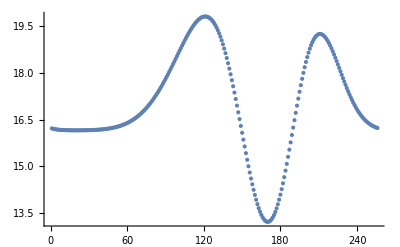

```mathematica
ListPlot[waveFunctionsRight⟦3⟧]
```

```mathematica
overlaps=testSolution⟦3⟧//TableForm
```

0.0560781 | -0.195449 | 0.410517 | 0.559661 | 0.529858
-0.195448 | 0.431643 | -0.491533 | -0.192225 | 0.232543
-0.410518 | 0.491534 | -0.103117 | 0.335931 | 0.274855
0.559665 | -0.192223 | -0.335933 | -0.187347 | 0.272443
0.529857 | 0.23255 | -0.274851 | 0.272446 | 0.189888

```mathematica
kappas=testSolution⟦11⟧//TableForm
```

0.22453 | 0.30141 | 0. | 0. | 0.
0.305758 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.